# Quick Start

Install latest version from Github:

```mathematica
PacletInstall[URL["https://github.com/GitHub-at-Brown/LongRunRisk/releases/download/pre-release-1.0.0/FernandoDuarte__LongRunRisk-1.0.0.paclet"],ForceVersionInstall->True]
```

PacletObject[…]

Load paclet:

```mathematica
Get["FernandoDuarte`LongRunRisk`"]
```

## Models

Display built-in models and some of their characteristics:

```mathematica
Models
```

```mathematica
Info[Models]
```

Pick a model to work with:

```mathematica
myModel = Models["BY"];
```

Get the names of all the exogenous and endogenous variables:

```mathematica
myModel["exogenousVarNames"]
myModel["endogenousVarNames"]
```

{x,pi,dc,sx,dd}

{wc,pd,bond,nombond,bondexcret,bondfw,bondfwspread,bondret,bondyield,excretc,excret,kappa0,kappa1,nombondexcret,nombondfw,nombondfwspread,nombondret,nombondyield,nomrf,nomsdf,retc,ret,rf,sdf}

Note that inflation is listed even though it is always identically zero in this model. Indeed, all models have inflation as one of the exogenous processes irrespective of whether it is always zero.

Get information about variables:

```mathematica
?x
```

```mathematica
?wc
```

```mathematica
?nombondfwspread
```

Show the dynamics of exogenous variables:

```mathematica
ToEquation[x[t], myModel]
ToEquation[dc[t+h], myModel]
ToEquation[dd[t-1,j], myModel]
```

rhox x[-1+t]+phix √(Esx^2+sx[-1+t]) eps[x][t]

muc+x[-1+h+t]+√(Esx^2+sx[-1+h+t]) eps[dc][h+t]

mud[j]+rhodx[j] x[-2+t]+phidxd[j] √(Esx^2+sx[-2+t]) eps[dd][-1+t,j]

Use Postfix notation:

```mathematica
dc[t]//ToEquation[myModel]
```

muc+x[-1+t]+√(Esx^2+sx[-1+t]) eps[dc][t]

Re-create the equations that gives the dynamics for the exogenous variables:

```mathematica
exoEq=Append[Map[Symbol[#][t+1]==ToEquation[Symbol[#][t+1],myModel] &,Most@myModel["exogenousVarNames"]],dd[t+1,i]==ToEquation[dd[t+1,i],myModel]];
Column[exoEq,Spacings->1.5]
```

x[1+t]==rhox x[t]+phix √(Esx^2+sx[t]) eps[x][1+t]
pi[1+t]==0
dc[1+t]==muc+x[t]+√(Esx^2+sx[t]) eps[dc][1+t]
sx[1+t]==vx sx[t]+phisxs eps[sx][1+t]
dd[1+t,i]==mud[i]+rhodx[i] x[t]+phidxd[i] √(Esx^2+sx[t]) eps[dd][1+t,i]

Show equations for some endogenous variables:

```mathematica
wc[t]//ToEquation[myModel]
pd[t,j] //ToEquation[myModel]
nombondfwspread[t,m] //ToEquation[myModel]
```

A[0]+A[2] sx[t]+A[1] x[t]

B[0][0]+x[t] B[1][1]+sx[t] B[2][2]

nombond[t,m,1]-nombondyield[t,1]

The variables that show up in the wealth-consumption ratio are the state variables of the model:

```mathematica
wc[t]//ToEquation[myModel]
stateVars=myModel["stateVars"][t]
```

A[0]+A[2] sx[t]+A[1] x[t]

{x[t],sx[t]}

Write endogenous variables in terms of exogenous variables or state variables:

```mathematica
ToExogenousVars[dc[t], myModel]
ToStateVars[dc[t], myModel]
```

dc[t]

muc+x[-1+t]+√(Esx^2+sx[-1+t]) eps[dc][t]

```mathematica
ToExogenousVars[ret[t,j], myModel]
ToStateVars[ret[t,j], myModel]
```

dd[t,j]-(ⅇ^Epd[j] Epd[j])/(1+ⅇ^Epd[j])+Log[1+ⅇ^Epd[j]]-B[0][0]-x[-1+t] B[1][1]-sx[-1+t] B[2][2]+(ⅇ^Epd[j] (B[0][0]+x[t] B[1][1]+sx[t] B[2][2]))/(1+ⅇ^Epd[j])

-(ⅇ^Epd[j] Epd[j])/(1+ⅇ^Epd[j])+Log[1+ⅇ^Epd[j]]+mud[j]+rhodx[j] x[-1+t]-B[0][0]-x[-1+t] B[1][1]-sx[-1+t] B[2][2]+(ⅇ^Epd[j] (B[0][0]+x[t] B[1][1]+sx[t] B[2][2]))/(1+ⅇ^Epd[j])+phidxd[j] √(Esx^2+sx[-1+t]) eps[dd][t,j]

Plug in the default numerical values for parameters using ReplaceRepeated:

```mathematica
delta//.myModel["params"]
theta //.myModel["params"]
myEq = ToEquation[x[t], myModel]
myEq //.myModel["params"]
```

0.998

-27.

rhox x[-1+t]+phix √(Esx^2+sx[-1+t]) eps[x][t]

0.979 x[-1+t]+0.044 √(0.00006084+sx[-1+t]) eps[x][t]

Use non-default values for some parameters:

```mathematica
myParams1 = {rhox->0.5};
myParams2 = {rhox->0.5, phix-> 0.01};

myEq //.myModel["params"]
myEq /. myParams1//.myModel["params"]
myEq //. myParams2 //.myModel["params"]
```

0.979 x[-1+t]+0.044 √(0.00006084+sx[-1+t]) eps[x][t]

0.5 x[-1+t]+0.044 √(0.00006084+sx[-1+t]) eps[x][t]

0.5 x[-1+t]+0.01 √(0.00006084+sx[-1+t]) eps[x][t]

Parameters are allowed to depend on each other. For example, we can pick psi=2, gamma=3 and then make theta=(1-gamma)/(1-1/psi):

```mathematica
myEq=ToEquation[sdf[t], myModel]
myEq//.{theta->(1-gamma)/(1-1/psi), psi->2, gamma->3}
```

-(theta dc[t])/psi+theta Log[delta]+(-1+theta) retc[t]

2 dc[t]-4 Log[delta]-5 retc[t]

Plugging in parameters only substitutes parameters that appear directly in an expression. Other constants remain symbolic:

```mathematica
ToEquation[wc[t], myModel]
ToEquation[wc[t], myModel]//.myModel["params"]
```

A[0]+A[2] sx[t]+A[1] x[t]

A[0]+A[2] sx[t]+A[1] x[t]

Format in LATEX:

```mathematica
dc[t] //ToTeX
wc[s] //ToTeX
pd[t+1,j] //ToTeX
nombondyield[t-1,m] //ToTeX
```

ToTeX[dc[t]]

ToTeX[wc[s]]

ToTeX[pd[1+t,j]]

ToTeX[nombondyield[-1+t,m]]

For some models, the original notation from the paper where the model was first published is available:

```mathematica
dc[t]  // ToPaper
```

ToPaper[dc[t]]

## Computing moments

### Unconditional moments

Compute unconditional means, variances and covariances of expressions:

```mathematica
Names["FernandoDuarte`LongRunRisk`*"]
```

{Corr,Cov,covLongBY,covLongDES,covLongNRC,Epd0,Ev,Ewc0,FindRootOptions,Growth,Info,Models,Moments,ProcessNewParameters,RecurrenceTableOptions,ToEquation,ToExogenousVars,ToNum,ToStateVars,UncondCorr,UncondCov,UncondE,UncondVar,Var,Var$,YieldCurve}

```mathematica
myModel = Models["NRC"];
UncondE[dc[t],myModel]
?UncondE
```

muc

```mathematica
UncondVar[dc[t],myModel]
?UncondVar
```

phic^2-mup^2 rhocp^2+2 Esg phip rhocp xic-((Esg^2+phig^2-Esg^2 rhog^2) xic^2)/((-1+rhog) (1+rhog))-(rhocp^2 (mup^2+phip^2-mup^2 rhop^2+2 phip rhop xip+xip^2))/((-1+rhop) (1+rhop))

```mathematica
UncondCov[dc[t],pi[t-1],myModel]//Simplify
UncondCorr[dc[t],pi[t-1],myModel] //Simplify
```

-(phip^2 rhocp-Esg phip (-1+rhop^2) xic+2 phip rhocp rhop xip+rhocp xip^2)/(-1+rhop^2)

(-phip^2 rhocp+Esg phip (-1+rhop^2) xic-2 phip rhocp rhop xip-rhocp xip^2)/((-1+rhop^2) √((phip^2+2 phip rhop xip+xip^2)/(1-rhop^2)) √(phic^2-mup^2 rhocp^2+2 Esg phip rhocp xic+(Esg^2-phig^2/(-1+rhog^2)) xic^2-(rhocp^2 (phip^2-mup^2 (-1+rhop^2)+2 phip rhop xip+xip^2))/(-1+rhop^2)))

Compare across models:

```mathematica
myOtherModel=Models["DES"];
UncondVar[dc[t],myModel] //Simplify
UncondVar[dc[t],myOtherModel] //Simplify
```

phic^2-mup^2 rhocp^2+2 Esg phip rhocp xic+(Esg^2-phig^2/(-1+rhog^2)) xic^2-(rhocp^2 (phip^2-mup^2 (-1+rhop^2)+2 phip rhop xip+xip^2))/(-1+rhop^2)

Esx^2 (1-phix^2/(-1+rhox^2))+(Esg^2-phig^2/(-1+rhog^2)) xic^2

Evaluate numerically:

```mathematica
UncondVar[dc[t],myModel] //. myModel["params"]
UncondVar[dc[t],myOtherModel] //. myOtherModel["params"]
```

0.0000515415

0.0000641552

```mathematica
UncondVar[dc[t],myModel] /.xic->0//. myModel["params"]
UncondVar[dc[t],myOtherModel] /.xic->0//. myOtherModel["params"]
```

4.2163×10^-6

3.39788×10^-6

### Conditional moments

Expected value conditional on information available at time t:

```mathematica
Ev[dc[t+1], t ,myModel]
Ev[eps["pi"][t+1], t, myModel]
Ev[eps["pi"][t+1]^2, t, myModel]
```

muc-mup rhocp+rhocp pi[t]+xic sg[-1+t] eps[pi][t]

0

1

Use different time periods:

```mathematica
Ev[dc[t+12], t+3, myModel]
Ev[dc[t], t-2, myModel]
```

muc-mup rhocp rhop^8+rhocp rhop^8 pi[3+t]+rhocp rhop^7 xip eps[pi][3+t]

muc-mup rhocp rhop+rhocp rhop pi[-2+t]+rhocp xip eps[pi][-2+t]

Conditional variances, covariances and correlations:

```mathematica
Var[dc[t],t-1,myModel]
Cov[wc[t],sg[t-1],t-2,myModel]
Corr[dc[t],pi[t-1],t-2,myModel]
```

phic^2

phig^2 rhog A[4]+2 Esg phig^2 rhog A[5]-2 Esg phig^2 rhog^3 A[5]+2 phig^2 rhog^3 A[5] sg[-2+t]

(phip^2 rhocp+phip xic sg[-2+t])/(√(phip^2) √(phic^2+phip^2 rhocp^2+2 phip rhocp xic sg[-2+t]+xic^2 sg[-2+t]^2))

Evaluate numerically

```mathematica
Corr[dc[t],pi[t-1],t-2,myModel]//. myModel["params"]//Simplify
```

(-0.000128307+0.198287 sg[-2+t])/(√(4.20479×10^-6-0.0000508833 sg[-2+t]+0.0393177 sg[-2+t]^2))

### Tables with moments

Some groups of moments can be shown in pre-defined tables:

```mathematica
Moments["stocks", myModel]
Moments["exogenousVars", myModel]
Moments["nomBonds", myModel]
Moments["varianceRatios", myModel]
```

### Time-aggregated moments

Compute first-order approximation of growth rates of time-aggregated variables:

```mathematica
Growth[dc,t]
Growth[dc,t,"TimeAggregation"->1,"numPeriods"->1]
Growth[dc,t,"TimeAggregation"->3,"numPeriods"->1]
Growth[dc,t,"TimeAggregation"->12,"numPeriods"->1]
```

dc[t]

dc[t]

1/3 (dc[-4+t]+2 dc[-3+t]+3 dc[-2+t]+2 dc[-1+t]+dc[t])

1/12 (dc[-22+t]+2 dc[-21+t]+3 dc[-20+t]+4 dc[-19+t]+5 dc[-18+t]+6 dc[-17+t]+7 dc[-16+t]+8 dc[-15+t]+9 dc[-14+t]+10 dc[-13+t]+11 dc[-12+t]+12 dc[-11+t]+11 dc[-10+t]+10 dc[-9+t]+9 dc[-8+t]+8 dc[-7+t]+7 dc[-6+t]+6 dc[-5+t]+5 dc[-4+t]+4 dc[-3+t]+3 dc[-2+t]+2 dc[-1+t]+dc[t])

The coefficients have the characteristic "tent shape".

Aggregate over more periods:

```mathematica
Growth[dc,t]
Growth[dc,t,"TimeAggregation"->1]
Growth[dc,t,"TimeAggregation"->3]
Growth[dc,t,"TimeAggregation"->12]
```

dc[t]

dc[t]

1/3 (dc[-4+t]+2 dc[-3+t]+3 dc[-2+t]+2 dc[-1+t]+dc[t])

1/12 (dc[-22+t]+2 dc[-21+t]+3 dc[-20+t]+4 dc[-19+t]+5 dc[-18+t]+6 dc[-17+t]+7 dc[-16+t]+8 dc[-15+t]+9 dc[-14+t]+10 dc[-13+t]+11 dc[-12+t]+12 dc[-11+t]+11 dc[-10+t]+10 dc[-9+t]+9 dc[-8+t]+8 dc[-7+t]+7 dc[-6+t]+6 dc[-5+t]+5 dc[-4+t]+4 dc[-3+t]+3 dc[-2+t]+2 dc[-1+t]+dc[t])

Compute cumulative growth rates over many periods:

```mathematica
Growth[dc,t,"TimeAggregation"->1,"numPeriods"->12] (*growth rate of monthly consumption (without any time aggregataion) cumulated over one year*)
Growth[dc,t,"TimeAggregation"->3,"numPeriods"->2](*cumulative growth rate over two quarters for consumption that is time-aggregated at a quarterly frequency*)
Growth[dc,t,"TimeAggregation"->12,"numPeriods"->2](*cumulative growth rate over two years for consumption that is time-aggregated at the annual frequency*)
```

The default is to interpret variables as flow variables:

```mathematica
Growth[dc,t,"TimeAggregation"->12,"numPeriods"->2]===
Growth[dc,t,"TimeAggregation"->12,"numPeriods"->2, "flowVariable"->True ]
```

True

To compute time-aggregated growth rates for stock variables, use "flowVariable"->False. The growth rate of a stock variable over a given period is independent of time-aggregation and can be computed exactly (without any approximations):

```mathematica
Growth[dc,t,"TimeAggregation"->12,"numPeriods"->1, "flowVariable"->False ]===
Growth[dc,t,"TimeAggregation"->3,"numPeriods"->4, "flowVariable"->False]===
Growth[dc,t,"TimeAggregation"->1,"numPeriods"->12, "flowVariable"->False ]
```

True

Use a power series expansion of Order `Order` to compute the approximation:

```mathematica
Growth[dc,t,"TimeAggregation"->3 , "Order"->2]
Growth[dc,t,"TimeAggregation"->3 , "Order"->3]
```

1/3 (dc[-4+t]+2 dc[-3+t]+3 dc[-2+t]+2 dc[-1+t]+dc[t])+1/9 (-dc[-4+t]^2-dc[-4+t] dc[-3+t]-dc[-3+t]^2+dc[-1+t]^2+dc[-1+t] dc[t]+dc[t]^2)

1/3 (dc[-4+t]+2 dc[-3+t]+3 dc[-2+t]+2 dc[-1+t]+dc[t])+1/9 (-dc[-4+t]^2-dc[-4+t] dc[-3+t]-dc[-3+t]^2+dc[-1+t]^2+dc[-1+t] dc[t]+dc[t]^2)+1/162 (2 dc[-4+t]^3+3 dc[-4+t]^2 dc[-3+t]-3 dc[-4+t] dc[-3+t]^2-2 dc[-3+t]^3-2 dc[-1+t]^3-3 dc[-1+t]^2 dc[t]+3 dc[-1+t] dc[t]^2+2 dc[t]^3)

Change the point around which the power series expansion is performed:

```mathematica
Growth[dc,t,"TimeAggregation"->3 ,"v0"->(0.0015 &)]
```

0.+0.332833 dc[-4+t]+0.666167 dc[-3+t]+dc[-2+t]+0.667167 dc[-1+t]+0.333833 dc[t]

## Model solutions

Coefficients of the wealth-consumption ratio

Display the expression for the wealth-consumption ratio:

```mathematica
myModel= Models["NRC"];
wcNRC = wc[t]//ToEquation[myModel]
```

A[0]+A[1] (-mup+pi[t])+A[4] (-Esg+sg[t])+A[5] (-Esg^2-phig^2/(1-rhog^2)+sg[t]^2)+A[3] eps[pi][t]+A[2] sg[-1+t] eps[pi][t]

Find the numerical value of the wealth-consumption ratio using the model's default parameters:

```mathematica
ToNum[wcNRC,myModel]
```

4.59417-0.124759 (-0.00327532+pi[t])+1.22397 (0.00624+sg[t])-26.0718 (-0.00119559+sg[t]^2)-0.000090171 eps[pi][t]-0.0991435 sg[-1+t] eps[pi][t]

```mathematica
%//Simplify
```

4.63338-0.124759 pi[t]+1.22397 sg[t]-26.0718 sg[t]^2-0.000090171 eps[pi][t]-0.0991435 sg[-1+t] eps[pi][t]

First find the solution, then apply it to any expression:

```mathematica
sol=ToNum["Rules",myModel];
Short[%,10]
```

{A[0]→4.59417,A[1]→-0.124759,A[2]→-0.0991435,A[3]→-0.000090171,A[4]→1.22397,A[5]→-26.0718,B[1][0]→4.72804,B[1][1]→3.54114,«1489»,rhodp[1]→0.709922,rhodp[2]→0.698934,rhodp[3]→-0.234447,xid[1]→-0.307616,xid[2]→0.108237,xid[3]→0.194176,Ewc→4.59417,Epd[FernandoDuarte`LongRunRisk`Tools`ToNumber`Private`ind$_]→B[FernandoDuarte`LongRunRisk`Tools`ToNumber`Private`ind$][0]}

```mathematica
wcNRC//.sol //Simplify
```

4.63338-0.124759 pi[t]+1.22397 sg[t]-26.0718 sg[t]^2-0.000090171 eps[pi][t]-0.0991435 sg[-1+t] eps[pi][t]

Use Postfix notation:

```mathematica
wcNRC // ToNum[myModel] //Simplify
```

4.63338-0.124759 pi[t]+1.22397 sg[t]-26.0718 sg[t]^2-0.000090171 eps[pi][t]-0.0991435 sg[-1+t] eps[pi][t]

Use non-default values for some parameters:

```mathematica
newSol=ToNum["Rules",myModel,{rhocp->-0.1}];
wcNRC  //. newSol // Simplify
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

4.58494-0.23889 pi[t]+2.28231 sg[t]-28.2176 sg[t]^2-0.000172557 eps[pi][t]-0.0991435 sg[-1+t] eps[pi][t]

Check that the solution is accurate despite the warning message issued by FindRoot:

```mathematica
newSol=ToNum["Rules",myModel,{rhocp->-0.1},"PrintResidualsNorm"->True]
wcNRC  //. newSol //Chop// Simplify
```

checks::norm: The norm of the residuals (errors) is 6.89789×10^-15

4.63338-0.124759 pi[t]+1.22397 sg[t]-26.0718 sg[t]^2-0.000090171 eps[pi][t]-0.0991435 sg[-1+t] eps[pi][t]

The norm of the residual is quite small (around 10^-14) so the solution is accurate.

Coefficients of price-dividend ratios

Display the expression for the price-dividend ratio for stock i:

```mathematica
pdNRC[i_]:=(pd[t,i]//ToEquation[myModel])
pdNRC[i]
```

B[i][0]+(-mup+pi[t]) B[i][1]+(-Esg+sg[t]) B[i][4]+(-Esg^2-phig^2/(1-rhog^2)+sg[t]^2) B[i][5]+sg[-1+t] B[i][2] eps[pi][t]+B[i][3] eps[pi][t]

Find the numerical value of the price-dividend ratio for stock 3 using the default parameters:

```mathematica
solPd=pdNRC[3]//.sol //Simplify
```

5.52319-1.02122 pi[t]-19.1369 sg[t]-111.316 sg[t]^2-0.000742548 eps[pi][t]+0.293319 sg[-1+t] eps[pi][t]

Display the expression for the price-dividend ratio of stock 1:

```mathematica
pd[t,1]//ToEquation[myModel]
```

B[1][0]+(-mup+pi[t]) B[1][1]+(-Esg+sg[t]) B[1][4]+(-Esg^2-phig^2/(1-rhog^2)+sg[t]^2) B[1][5]+sg[-1+t] B[1][2] eps[pi][t]+B[1][3] eps[pi][t]

Use non-default values for some parameters:

```mathematica
newSolPd=pdNRC[3]//.newSol //Simplify
```

5.86893-0.907937 pi[t]-12.8488 sg[t]-89.2889 sg[t]^2-0.000660934 eps[pi][t]+0.293319 sg[-1+t] eps[pi][t]

Display a comparison

```mathematica
ResourceFunction["NiceGrid"][
	{
	{"rhocp",rhocp/.sol,rhocp/.newSol},
	{"wc",wcNRC  //. sol ,wcNRC  //. newSol},
	{"pd",pdNRC[3]  //. sol ,pdNRC[3]  //. newSol }
}
]// Simplify
```

rhocp | -0.0521066 | -0.1
wc | 4.63338-0.124759 pi[t]+1.22397 sg[t]-26.0718 sg[t]^2-0.000090171 eps[pi][t]-0.0991435 sg[-1+t] eps[pi][t] | 4.58494-0.23889 pi[t]+2.28232 sg[t]-28.2176 sg[t]^2-0.000172557 eps[pi][t]-0.0991435 sg[-1+t] eps[pi][t]
pd | 5.52319-1.02122 pi[t]-19.1369 sg[t]-111.316 sg[t]^2-0.000742548 eps[pi][t]+0.293319 sg[-1+t] eps[pi][t] | 5.86893-0.907937 pi[t]-12.8488 sg[t]-89.2889 sg[t]^2-0.000660934 eps[pi][t]+0.293319 sg[-1+t] eps[pi][t]

Coefficients of bond prices

The price of real and nominal bonds is given by:

```mathematica
b=bond[t,m]//ToEquation[myModel]
nb=nombond[t,m]//ToEquation[myModel]
```

R[m][0]+(-mup+pi[t]) R[m][1]+sg[-1+t] eps[pi][t] R[m][2]+eps[pi][t] R[m][3]+(-Esg+sg[t]) R[m][4]+(-Esg^2-phig^2/(1-rhog^2)+sg[t]^2) R[m][5]

P[m][0]+(-mup+pi[t]) P[m][1]+sg[-1+t] eps[pi][t] P[m][2]+eps[pi][t] P[m][3]+(-Esg+sg[t]) P[m][4]+(-Esg^2-phig^2/(1-rhog^2)+sg[t]^2) P[m][5]

Evaluate numerically for a maturity of 12 months:

```mathematica
b/.m->12//.sol//Simplify
nb/.m->12//.sol//Simplify
```

-0.127234+0.120924 pi[t]-0.248864 sg[t]+9.67776 sg[t]^2+0.0000866674 eps[pi][t]+0.0991435 sg[-1+t] eps[pi][t]

-0.154953-3.58834 pi[t]-0.0189702 sg[t]+9.67776 sg[t]^2-0.00330188 eps[pi][t]+0.0991435 sg[-1+t] eps[pi][t]

Get the yield curve:

```mathematica
meanYield=Simplify@UncondE[bondyield[t,m],myModel]
meanNomYield=Simplify@UncondE[nombondyield[t,m],myModel]
```

-(R[m][0])/m

-(P[m][0])/m

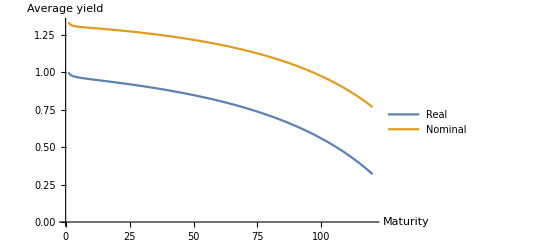

```mathematica
yieldCurve=Table[{m,100*meanYield},{m,1,120}]//.sol;
nomYieldCurve=Table[{m,100*meanNomYield},{m,1,120}]//.sol;

ListLinePlot[{yieldCurve,nomYieldCurve},PlotLegends->{"Real","Nominal"},AxesLabel->{"Maturity","Average yield"}]
```

Make an interactive plot:

```mathematica
rhocpRange = {{rhocpM,rhocp/.myModel["params"]},-0.5,0.5};
psiRange =  {{psiM,psi/.myModel["params"]},0.8,2.5};
sol0 = ToNum["Rules",myModel];

Manipulate[
sol=Quiet@ToNum["Rules",myModel,{rhocp->rhocpM, psi->psiM},sol0];
nomYields=Table[{m,100*meanNomYield},{m,1,60}]//.sol;
nomYieldCurve=ListLinePlot[nomYields]
,Evaluate@rhocpRange,Evaluate@psiRange]
```

## Nominal-real covariance

Conditional covariance between nominal bond yields and aggregate market stock returns (stock 1) at different maturities:

```mathematica
nrc=Cov[100*nombondyield[t+1,m],100*ret[t+1,1],t-1,myModel];
```

Plot average nrc across maturities:

```mathematica
uncondEnrc=UncondE[nrc,myModel]//Simplify;
```

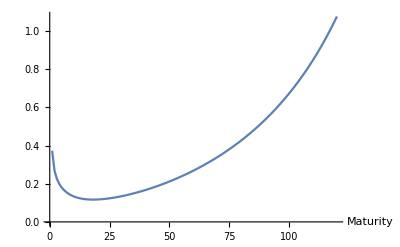

```mathematica
nrcCurve=Table[{m,uncondEnrc},{m,1,120}]//.sol;
ListLinePlot[nrcCurve,AxesLabel->{"Maturity",Automatic}]
```

## Variance Ratios for Inflation

The variance ratio for inflation is:

```mathematica
varianceRatio[horizon_,timeAggregation_,model_]:=UncondVar[Growth[pi,t, "numPeriods"->horizon, "TimeAggregation"-> timeAggregation],model]/(horizon*UncondVar[Growth[pi,t, "numPeriods"->1, "TimeAggregation"-> timeAggregation],model])
```

Make a plot of variance ratios at different horizons:

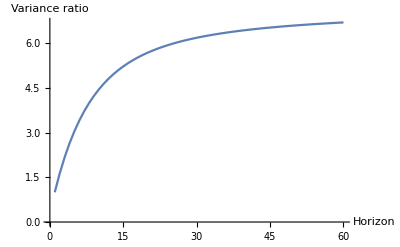

```mathematica
infVR=Table[varianceRatio[h,1,myModel],{h,1,60}]//.myModel["params"];
ListLinePlot[infVR,AxesLabel->{"Horizon","Variance ratio"}]
```

## Returns

Make an interactive plot:

```mathematica
rhocpRange = {{rhocpM,rhocp/.myModel["params"]},-0.5,0.5};
psiRange =  {{psiM,psi/.myModel["params"]},0.8,2.5};
sol0 = ToNum["Rules",myModel];
stockRet = 100*12*uncondE[ret[t,1],myModel];
nomBondRet =100*12* uncondE[nombondret[t,m],myModel];

Manipulate[
sol=Quiet@ToNum["Rules",myModel,{rhocp->rhocpM, psi->psiM},sol0];
nomRetCurve=Table[{m,nomBondRet},{m,1,60}]//.sol;
p1=ListLinePlot[nomRetCurve,PlotLabel->"Nominal Bond Returns",AxesLabel->{"Maturity","Annualized returns"},ImageSize->Medium];
Grid[{
{Show[p1]},
{},
{"Aggregate Market Returns: "<>ToString[stockRet//.sol]}
},Dividers->{None,{1->None,3->Black}}]

,Evaluate@rhocpRange,Evaluate@psiRange,ContentSize ->Automatic]
```

Related Guides

Main Guide

Related Tech Notes

Time Aggregation
Interacting with Models

## Metadata

### Categorization

Tech Note

FernandoDuarte/LongRunRisk

FernandoDuarte`LongRunRisk`

FernandoDuarte/LongRunRisk/tutorial/Workflow

### Keywords